```mathematica
(*css zebrafinch model*)
(*recursions*)
ns := Na ba pa + Nn bn pn;
nh:= Na ba (1-pa) + Nn bn (1-pn);
NNa :=ns vs((1-lsO) vI z +lsO qO ) + nh vh((1-lhO) vI z +lhO qO );
NNn :=ns vs((1-lsO) vI (1-z)+lsO(1- qO) ) + nh vh((1-lhO) vI (1-z)+lhO(1- qO) );
qO := (1-u)(Na/(Na +Nn));
```

```mathematica
AA:=({{0, 0, ba pa, bn pn}, {0, 0, ba(1-pa), bn(1-pn)}, {vs((1-lsO) vI z +lsO qO ), vh((1-lhO) vI z +lhO qO ), 0, 0}, {vs((1-lsO) vI (1-z)+lsO(1- qO) ), vh((1-lhO) vI (1-z)+lhO(1- qO) ), 0, 0}})
```

```mathematica
NN = FullSimplify[NNn + NNa];
```

```mathematica
FFa=FullSimplify[NNa/NN/.{Na->Fa N0,Nn->(1-Fa)N0}];
```

```mathematica
FFn=FullSimplify[NNn/NN/.{Na->Fa N0,Nn->(1-Fa)N0}];
```

```mathematica
Simplify[FFn+FFa]
```

1

```mathematica
Fasols=Solve[FFa==Fa,Fa]
```

{{Fa→(bn lhO u vh-bn lhO pn u vh+bn vh vI-bn lhO vh vI-bn pn vh vI+bn lhO pn vh vI+bn lsO pn u vs+bn pn vI vs-bn lsO pn vI vs-ba vh vI z+bn vh vI z+ba lhO vh vI z-bn lhO vh vI z+ba pa vh vI z-ba lhO pa vh vI z-bn pn vh vI z+bn lhO pn vh vI z-ba pa vI vs z+ba lsO pa vI vs z+bn pn vI vs z-bn lsO pn vI vs z-√(-4 (-ba lhO u vh+bn lhO u vh+ba lhO pa u vh-bn lhO pn u vh-ba vh vI+bn vh vI+ba lhO vh vI-bn lhO vh vI+ba pa vh vI-ba lhO pa vh vI-bn pn vh vI+bn lhO pn vh vI-ba lsO pa u vs+bn lsO pn u vs-ba pa vI vs+ba lsO pa vI vs+bn pn vI vs-bn lsO pn vI vs) (bn vh vI z-bn lhO vh vI z-bn pn vh vI z+bn lhO pn vh vI z+bn pn vI vs z-bn lsO pn vI vs z)+(-bn lhO u vh+bn lhO pn u vh-bn vh vI+bn lhO vh vI+bn pn vh vI-bn lhO pn vh vI-bn lsO pn u vs-bn pn vI vs+bn lsO pn vI vs+ba vh vI z-bn vh vI z-ba lhO vh vI z+bn lhO vh vI z-ba pa vh vI z+ba lhO pa vh vI z+bn pn vh vI z-bn lhO pn vh vI z+ba pa vI vs z-ba lsO pa vI vs z-bn pn vI vs z+bn lsO pn vI vs z)^2))/(2 (-ba lhO u vh+bn lhO u vh+ba lhO pa u vh-bn lhO pn u vh-ba vh vI+bn vh vI+ba lhO vh vI-bn lhO vh vI+ba pa vh vI-ba lhO pa vh vI-bn pn vh vI+bn lhO pn vh vI-ba lsO pa u vs+bn lsO pn u vs-ba pa vI vs+ba lsO pa vI vs+bn pn vI vs-bn lsO pn vI vs))},{Fa→(bn lhO u vh-bn lhO pn u vh+bn vh vI-bn lhO vh vI-bn pn vh vI+bn lhO pn vh vI+bn lsO pn u vs+bn pn vI vs-bn lsO pn vI vs-ba vh vI z+bn vh vI z+ba lhO vh vI z-bn lhO vh vI z+ba pa vh vI z-ba lhO pa vh vI z-bn pn vh vI z+bn lhO pn vh vI z-ba pa vI vs z+ba lsO pa vI vs z+bn pn vI vs z-bn lsO pn vI vs z+√(-4 (-ba lhO u vh+bn lhO u vh+ba lhO pa u vh-bn lhO pn u vh-ba vh vI+bn vh vI+ba lhO vh vI-bn lhO vh vI+ba pa vh vI-ba lhO pa vh vI-bn pn vh vI+bn lhO pn vh vI-ba lsO pa u vs+bn lsO pn u vs-ba pa vI vs+ba lsO pa vI vs+bn pn vI vs-bn lsO pn vI vs) (bn vh vI z-bn lhO vh vI z-bn pn vh vI z+bn lhO pn vh vI z+bn pn vI vs z-bn lsO pn vI vs z)+(-bn lhO u vh+bn lhO pn u vh-bn vh vI+bn lhO vh vI+bn pn vh vI-bn lhO pn vh vI-bn lsO pn u vs-bn pn vI vs+bn lsO pn vI vs+ba vh vI z-bn vh vI z-ba lhO vh vI z+bn lhO vh vI z-ba pa vh vI z+ba lhO pa vh vI z+bn pn vh vI z-bn lhO pn vh vI z+ba pa vI vs z-ba lsO pa vI vs z-bn pn vI vs z+bn lsO pn vI vs z)^2))/(2 (-ba lhO u vh+bn lhO u vh+ba lhO pa u vh-bn lhO pn u vh-ba vh vI+bn vh vI+ba lhO vh vI-bn lhO vh vI+ba pa vh vI-ba lhO pa vh vI-bn pn vh vI+bn lhO pn vh vI-ba lsO pa u vs+bn lsO pn u vs-ba pa vI vs+ba lsO pa vI vs+bn pn vI vs-bn lsO pn vI vs))}}

```mathematica
test = {lsO-> 0.2 ,lhO-> 0.8};
subs = {ba->3,bn->1,z->0.8,vs->0.4,vh->0.9,vI->0.8  ,u->0.1, pa-> 0, pn-> 1};
```

```mathematica
Fasols[[1,1,2]]/.subs/.test (*check it is stable qhat with values, select positive q-hat*)
 Fasols/.subs
```

0.587291

{{Fa→(-1.152+1.728 lhO-√(-4 (-1.84+1.89 lhO-0.28 lsO) (0.256-0.256 lsO)+(1.152-1.728 lhO+0.536 lsO)^2)-0.536 lsO)/(2 (-1.84+1.89 lhO-0.28 lsO))},{Fa→(-1.152+1.728 lhO+√(-4 (-1.84+1.89 lhO-0.28 lsO) (0.256-0.256 lsO)+(1.152-1.728 lhO+0.536 lsO)^2)-0.536 lsO)/(2 (-1.84+1.89 lhO-0.28 lsO))}}

```mathematica
QHAT= Simplify[Fasols[[1,1,2]]];
```

```mathematica
AA2=Simplify[AA/.{Na->QHAT,Nn->(1-QHAT)}/.subs];
```

```mathematica
LL=Eigenvalues[AA2];
```

```mathematica
LL
```

{1/(-184.+189. lhO-28. lsO)0.004 Root[-67.3828-2.0049×10^18 lhO+7.7222×10^18 lhO^2-1.1104×10^19 lhO^3+7.06013×10^18 lhO^4-1.67337×10^18 lhO^5+2.0049×10^18 lsO-8.60132×10^18 lhO lsO+1.35778×10^19 lhO^2 lsO-9.35946×10^18 lhO^3 lsO+2.3779×10^18 lhO^4 lsO-414.313 lhO^5 lsO+8.7912×10^17 lsO^2-2.59654×10^18 lhO lsO^2+2.51575×10^18 lhO^2 lsO^2-7.97291×10^17 lhO^3 lsO^2+124.731 lhO^4 lsO^2+1.22773×10^17 lsO^3-2.20971×10^17 lhO lsO^3+9.5623×10^16 lhO^2 lsO^3-17.3594 lhO^3 lsO^3+4.55281×10^15 lsO^4-2.73311×10^15 lhO lsO^4+2.03121 lhO^2 lsO^4-1.27431×10^14 lsO^5-0.125908 lhO lsO^5+9.46106×10^17 lhO √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-2.91545×10^18 lhO^2 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+2.99467×10^18 lhO^3 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-1.02535×10^18 lhO^4 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-9.46106×10^17 lsO √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+3.34736×10^18 lhO lsO √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-3.88198×10^18 lhO^2 lsO √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+1.48106×10^18 lhO^3 lsO √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-138.428 lhO^4 lsO √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-4.31918×10^17 lsO^2 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+9.53036×10^17 lhO lsO^2 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-5.23223×10^17 lhO^2 lsO^2 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+55.1147 lhO^3 lsO^2 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-6.57266×10^16 lsO^3 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+7.08467×10^16 lhO lsO^3 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-4.04549 lhO^2 lsO^3 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-3.33396×10^15 lsO^4 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-0.160217 lhO lsO^4 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+(-3.79187×10^9+9.83664×10^9 lhO-7.44455×10^9 lhO^2+1.37781×10^9 lhO^3-1.62656×10^9 lsO+2.16232×10^9 lhO lsO-3.89104×10^8 lhO^2 lsO-1.56952×10^8 lsO^2+2.457×10^7 lhO lsO^2+420000. lsO^3-1.39725×10^9 lhO √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+1.43522×10^9 lhO^2 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+2.07×10^8 lsO √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-4.2525×10^8 lhO lsO √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+3.15×10^7 lsO^2 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)) #1^2+#1^4&,1],1/(-184.+189. lhO-28. lsO)0.004 Root[-67.3828-2.0049×10^18 lhO+7.7222×10^18 lhO^2-1.1104×10^19 lhO^3+7.06013×10^18 lhO^4-1.67337×10^18 lhO^5+2.0049×10^18 lsO-8.60132×10^18 lhO lsO+1.35778×10^19 lhO^2 lsO-9.35946×10^18 lhO^3 lsO+2.3779×10^18 lhO^4 lsO-414.313 lhO^5 lsO+8.7912×10^17 lsO^2-2.59654×10^18 lhO lsO^2+2.51575×10^18 lhO^2 lsO^2-7.97291×10^17 lhO^3 lsO^2+124.731 lhO^4 lsO^2+1.22773×10^17 lsO^3-2.20971×10^17 lhO lsO^3+9.5623×10^16 lhO^2 lsO^3-17.3594 lhO^3 lsO^3+4.55281×10^15 lsO^4-2.73311×10^15 lhO lsO^4+2.03121 lhO^2 lsO^4-1.27431×10^14 lsO^5-0.125908 lhO lsO^5+9.46106×10^17 lhO √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-2.91545×10^18 lhO^2 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+2.99467×10^18 lhO^3 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-1.02535×10^18 lhO^4 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-9.46106×10^17 lsO √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+3.34736×10^18 lhO lsO √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-3.88198×10^18 lhO^2 lsO √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+1.48106×10^18 lhO^3 lsO √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-138.428 lhO^4 lsO √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-4.31918×10^17 lsO^2 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+9.53036×10^17 lhO lsO^2 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-5.23223×10^17 lhO^2 lsO^2 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+55.1147 lhO^3 lsO^2 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-6.57266×10^16 lsO^3 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+7.08467×10^16 lhO lsO^3 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-4.04549 lhO^2 lsO^3 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-3.33396×10^15 lsO^4 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-0.160217 lhO lsO^4 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+(-3.79187×10^9+9.83664×10^9 lhO-7.44455×10^9 lhO^2+1.37781×10^9 lhO^3-1.62656×10^9 lsO+2.16232×10^9 lhO lsO-3.89104×10^8 lhO^2 lsO-1.56952×10^8 lsO^2+2.457×10^7 lhO lsO^2+420000. lsO^3-1.39725×10^9 lhO √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+1.43522×10^9 lhO^2 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+2.07×10^8 lsO √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-4.2525×10^8 lhO lsO √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+3.15×10^7 lsO^2 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)) #1^2+#1^4&,2],1/(-184.+189. lhO-28. lsO)0.004 Root[-67.3828-2.0049×10^18 lhO+7.7222×10^18 lhO^2-1.1104×10^19 lhO^3+7.06013×10^18 lhO^4-1.67337×10^18 lhO^5+2.0049×10^18 lsO-8.60132×10^18 lhO lsO+1.35778×10^19 lhO^2 lsO-9.35946×10^18 lhO^3 lsO+2.3779×10^18 lhO^4 lsO-414.313 lhO^5 lsO+8.7912×10^17 lsO^2-2.59654×10^18 lhO lsO^2+2.51575×10^18 lhO^2 lsO^2-7.97291×10^17 lhO^3 lsO^2+124.731 lhO^4 lsO^2+1.22773×10^17 lsO^3-2.20971×10^17 lhO lsO^3+9.5623×10^16 lhO^2 lsO^3-17.3594 lhO^3 lsO^3+4.55281×10^15 lsO^4-2.73311×10^15 lhO lsO^4+2.03121 lhO^2 lsO^4-1.27431×10^14 lsO^5-0.125908 lhO lsO^5+9.46106×10^17 lhO √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-2.91545×10^18 lhO^2 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+2.99467×10^18 lhO^3 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-1.02535×10^18 lhO^4 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-9.46106×10^17 lsO √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+3.34736×10^18 lhO lsO √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-3.88198×10^18 lhO^2 lsO √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+1.48106×10^18 lhO^3 lsO √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-138.428 lhO^4 lsO √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-4.31918×10^17 lsO^2 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+9.53036×10^17 lhO lsO^2 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-5.23223×10^17 lhO^2 lsO^2 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+55.1147 lhO^3 lsO^2 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-6.57266×10^16 lsO^3 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+7.08467×10^16 lhO lsO^3 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-4.04549 lhO^2 lsO^3 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-3.33396×10^15 lsO^4 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-0.160217 lhO lsO^4 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+(-3.79187×10^9+9.83664×10^9 lhO-7.44455×10^9 lhO^2+1.37781×10^9 lhO^3-1.62656×10^9 lsO+2.16232×10^9 lhO lsO-3.89104×10^8 lhO^2 lsO-1.56952×10^8 lsO^2+2.457×10^7 lhO lsO^2+420000. lsO^3-1.39725×10^9 lhO √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+1.43522×10^9 lhO^2 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+2.07×10^8 lsO √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-4.2525×10^8 lhO lsO √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+3.15×10^7 lsO^2 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)) #1^2+#1^4&,3],1/(-184.+189. lhO-28. lsO)0.004 Root[-67.3828-2.0049×10^18 lhO+7.7222×10^18 lhO^2-1.1104×10^19 lhO^3+7.06013×10^18 lhO^4-1.67337×10^18 lhO^5+2.0049×10^18 lsO-8.60132×10^18 lhO lsO+1.35778×10^19 lhO^2 lsO-9.35946×10^18 lhO^3 lsO+2.3779×10^18 lhO^4 lsO-414.313 lhO^5 lsO+8.7912×10^17 lsO^2-2.59654×10^18 lhO lsO^2+2.51575×10^18 lhO^2 lsO^2-7.97291×10^17 lhO^3 lsO^2+124.731 lhO^4 lsO^2+1.22773×10^17 lsO^3-2.20971×10^17 lhO lsO^3+9.5623×10^16 lhO^2 lsO^3-17.3594 lhO^3 lsO^3+4.55281×10^15 lsO^4-2.73311×10^15 lhO lsO^4+2.03121 lhO^2 lsO^4-1.27431×10^14 lsO^5-0.125908 lhO lsO^5+9.46106×10^17 lhO √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-2.91545×10^18 lhO^2 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+2.99467×10^18 lhO^3 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-1.02535×10^18 lhO^4 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-9.46106×10^17 lsO √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+3.34736×10^18 lhO lsO √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-3.88198×10^18 lhO^2 lsO √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+1.48106×10^18 lhO^3 lsO √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-138.428 lhO^4 lsO √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-4.31918×10^17 lsO^2 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+9.53036×10^17 lhO lsO^2 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-5.23223×10^17 lhO^2 lsO^2 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+55.1147 lhO^3 lsO^2 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-6.57266×10^16 lsO^3 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+7.08467×10^16 lhO lsO^3 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-4.04549 lhO^2 lsO^3 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-3.33396×10^15 lsO^4 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-0.160217 lhO lsO^4 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+(-3.79187×10^9+9.83664×10^9 lhO-7.44455×10^9 lhO^2+1.37781×10^9 lhO^3-1.62656×10^9 lsO+2.16232×10^9 lhO lsO-3.89104×10^8 lhO^2 lsO-1.56952×10^8 lsO^2+2.457×10^7 lhO lsO^2+420000. lsO^3-1.39725×10^9 lhO √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+1.43522×10^9 lhO^2 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+2.07×10^8 lsO √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)-4.2525×10^8 lhO lsO √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)+3.15×10^7 lsO^2 √(3.21126-5.91667 lhO+2.98598 lhO^2-0.362496 lsO+0.082944 lhO lsO+0.000576 lsO^2)) #1^2+#1^4&,4]}

```mathematica
LV=Eigenvectors[AA2]
```

Eigenvectors::eivec0: Unable to find all eigenvectors.

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
LL/.subs /.test  (*sub in rando qhat value to identify positive eigen values*)
```

{1.28877,-1.28877,0.+0.291067 ⅈ,0.-0.291067 ⅈ}

```mathematica
(*eigenvectors give one ratios of stage/stress classes*) 
LV/.subs /.test
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
(*isolate dominant eigenvalue*)
Lambda[ lsO_, lhO_]:=LL[[1]];
```

```mathematica
(*use Lambda1 for general soln with pa and pn as parameters*)
DlsO=D[Lambda[lsO, lhO],lsO]/.subs;
```

```mathematica
DlhO=D[Lambda[lsO, lhO],lhO] /.subs;
```

```mathematica
(*try and graph*)

lsOstart=0.01;
lhOstart=0.01;
imax=1000;
lsItab=Table[0,{i,imax}];
lhItab=Table[0,{i,imax}];
lsOtab=Table[0,{i,imax}];
lhOtab=Table[0,{i,imax}];
DlsOtab=Table[0,{i,imax}];
DlhOtab=Table[0,{i,imax}];
delta=0.04;
lsOtab[[1]]=lsOstart;
lhOtab[[1]]=lhOstart;

DlsOtab[[1]]=DlsO/.subs/.{lsO->lsOstart,lhO->lhOstart};
DlhOtab[[1]]=DlhO/.subs/.{lsO->lsOstart,lhO->lhOstart};
```

```mathematica
For[i=2,i<imax,i++,{

lsOtab[[i]]=lsOtab[[i-1]]  + delta DlsO/.subs/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lsOtab[[i]]=If[lsOtab[[i]]>1,1,lsOtab[[i]]];
lsOtab[[i]]=If[lsOtab[[i]]<0,0,lsOtab[[i]]];

lhOtab[[i]]=lhOtab[[i-1]]  + delta DlhO/.subs/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lhOtab[[i]]=If[lhOtab[[i]]>1,1,lhOtab[[i]]];
lhOtab[[i]]=If[lhOtab[[i]]<0,0,lhOtab[[i]]];

DlsOtab[[i]]=DlsO/.subs/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
DlhOtab[[i]]=DlhO/.subs/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
}];
```

```mathematica
lsItab = 1-lsOtab;
lhItab = 1-lhOtab;
```

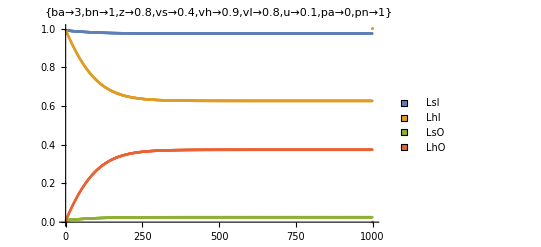

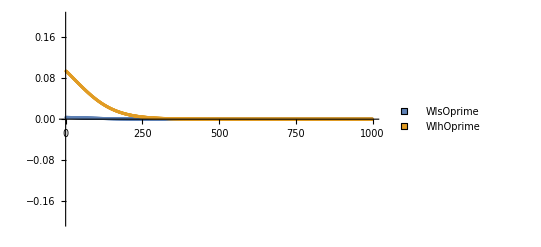

```mathematica
ListPlot[{lsItab,lhItab,lsOtab,lhOtab},PlotRange->{All,{0,1}},PlotLabel->subs, PlotLegends->PointLegend[{LsI,LhI,LsO,LhO},LegendMarkers->Graphics[Rectangle[]]]] 
ListPlot[{DlsOtab,DlhOtab},PlotRange->{All,{-0.2,0.2}},PlotLegends->PointLegend[{WlsOprime,WlhOprime},LegendMarkers->Graphics[Rectangle[]]]]
```